## Associated Code

```mathematica
bresenhamLine[p0_,p1_]:=Module[{dx,dy,sx,sy,err,newp},{dx,dy}=Abs[p1-p0];
{sx,sy}=Sign[p1-p0];
err=dx-dy;
newp[{x_,y_}]:=With[{e2=2 err},{If[e2>-dy,err-=dy;x+sx,x],If[e2<dx,err+=dx;y+sy,y]}];
NestWhileList[newp,p0,#=!=p1&,1]];
```

```mathematica
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(*here we transpose the image data*)
{nx,ny}=Dimensions[imd];(*dimensions of the image*)
points=Tuples[{Range[nx],Reverse@Range[ny]}];(*x-y coordinates on the image*)
weights=Flatten[imd];(*vector of imagedata*)
centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(*here we calculate the x-y coordinate of the center of mass*)
pointsCom=(Subtract[#,centerOfMass]&/@points) weights;(*we subtract from each point the center of mass.This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids.We multiply this resulting matrix with the intensity vector.This gives us a vector consisting of two coordinates which are x,y displacments from centroid for each point in the grid*)diag=Total[(#.#)&/@pointsCom];(*sum of the {x,y}.{x,y} from above. gives a single value*)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}];(*inertia*)
{v1,v2}=Eigenvectors[inertia];(*extracting eigenvectors from inertia*)
(*Print["center of Mass: ",centerOfMass,"\n","pt1 : ",v1+centerOfMass,"\n","pt2 : ",v2+centerOfMass];*)If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},
{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},
Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]
];
{centerOfMass,v1,v2}];

maskToRegion[mask_]:=Block[{pixelvaluepos,tour,pixelposordered},
pixelvaluepos=PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[pixelvaluepos];
pixelposordered=Part[pixelvaluepos,tour];
{pixelposordered,BoundaryMeshRegion[N@pixelvaluepos,Line@tour]}
];

bisectMask[mask_,option_:False]:=Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,temp,pt1,pt2,list,trimList,npixelordered,nf,ptslocation,firstPreMask,secondPreMask,dim,pt3,pt4},
dim=First@ImageDimensions[mask];
{centerofMass,v1,v2}=findSym[mask];
{pixelordered,ℛ1}=maskToRegion[mask];

ℛ2=InfiniteLine[{centerofMass,centerofMass+v2}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:>arg]&);

trimList[ls_]:=Module[{p=ls,pairs,firstelem=First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt3,pt4}=trimList[list]/.trimList[arg__]:>arg;

ℛ2=InfiniteLine[{centerofMass,centerofMass+v1}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:>arg]&);
{pt1,pt2}=trimList[list]/.trimList[arg__]:>arg;

If[option,
temp=Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]]
];
npixelordered=N@pixelordered;
nf=Nearest[npixelordered];
ptslocation=Flatten@Position[npixelordered,Flatten@nf[pt1]|Flatten@nf[pt2]];
firstPreMask=PadRight[#,Length@#+1,#]&@Part[pixelordered,First@ptslocation;;Last@ptslocation]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;
secondPreMask=Join[pixelordered[[;;First@ptslocation+1]],pixelordered[[Last@ptslocation+1;;]]]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;
Switch[option,True,Join[{temp},{centerofMass},pt1,pt2,pt3,pt4],_,Join[{centerofMass},pt1,pt2,pt3,pt4]]
];
```

# Maps

```mathematica
(* imports *)
images=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - cropped.tif"][[1;;160]];
masks1=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - masks.tif"][[1;;160]];
mask1=masks1[[125]];
```

```mathematica
masks2=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\D11 - masks.tiff"][[;;160]];
mask2=masks2[[-1]];
Clear[masks2];
```

```mathematica
masks3=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\F10 - masks.tiff"];
mask3=masks3[[-1]];
Clear[masks3];
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx";
res1=sim;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim3-filter20.mx";
res2=sim;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim2.mx";
res3=sim;
```

```mathematica
Length/@{res1,res2,res3}
```

{159,159,150}

```mathematica
meanFlowField[flowfield_]:=Normal@GroupBy[Flatten[Thread/@flowfield,1],First->Last,Mean]/.Rule-> List;
```

```mathematica
(*m1 is reference to which other images need to be aligned to*)
```

```mathematica
(m1=ImagePad[mask1,{{67,68},{69,69}}])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(m2=ImagePad[ImageRotate[mask2,-2.2Pi/5],{{55,55},{36,36}}])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(m3=ImageRotate[mask3,-Pi/4])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
SameQ@@ImageDimensions/@{m1,m2,m3}
```

True

```mathematica
{HighlightImage[m1,m2,ImageSize->Small],HighlightImage[m1,m3,ImageSize->Small]}
```

{-Graphics-,-Graphics-}

```mathematica
(align1=ImageAlign[m1,m2,Method->"MeanSquareGradientDescent",
TransformationClass->"Affine",Background->0])//Image[#,ImageSize->Small]&
```

-Graphics-

```mathematica
(align2=ImageAlign[m1,m3,Method->"MeanSquareGradientDescent",
TransformationClass->"Affine",Background->0])//Image[#,ImageSize->Small]&
```

-Graphics-

```mathematica
HighlightImage[m1,{Red,align1,Blue,align2},ImageSize->200]
```

-Graphics-

```mathematica
{err1,transF1}=FindGeometricTransform[m1,m2,Method->{"ImageAlign","MeanSquareGradientDescent"},TransformationClass->"Affine"]
```

{0.00168849,TransformationFunction[(1.17238 | 0.163917 | -64.0925
0.0102533 | 1.00887 | -3.06669
0. | 0. | 1.)]}

```mathematica
{err2,transF2}=FindGeometricTransform[m1,m3,Method->{"ImageAlign","MeanSquareGradientDescent"},TransformationClass->"Affine"]
```

{0.00153101,TransformationFunction[(1.07358 | 0.106041 | -40.7052
0.0103637 | 1.0062 | -2.95138
0. | 0. | 1.)]}

```mathematica
interpPeri1=ImageMeasurements[m1,"PerimeterPositions"][[1]];
interpPeri2=ImageMeasurements[m2,"PerimeterPositions"][[1]];
interpPeri3=ImageMeasurements[m3,"PerimeterPositions"][[1]];
```

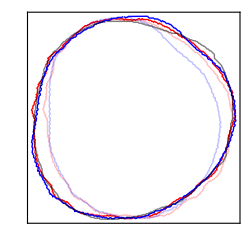

```mathematica
Graphics[
{{Thick,Red,Opacity[0.25],Line@interpPeri3},{Red,Thick,Line[transF2@interpPeri3]},
(*{GrayLevel[0.4],Arrowheads[Small],Arrow[{#,transF2@#}&/@interpPeri2]},*)
{Thick,Blue,Opacity[0.25],Line@interpPeri2},{Thick,Blue,Line[transF1@interpPeri2]},
{Thick,Opacity[0.5],Black,Line@interpPeri1}},PlotRange->All,ImageSize->250,
Frame->True,FrameTicks->False
]
```

```mathematica
(* till above we have a transformation matrix (affine transformation class) obtained from image masks that we can use to transform the points from one image to another *)
```

```mathematica
{meanflow1,meanflow2,meanflow3}=meanFlowField/@{res1,res2,res3};
```

```mathematica
(* we have mean flow fields for all the three aggregates *)
```

```mathematica
{pts1,vec1}=Transpose@meanflow1;
{pts2,vec2}=Transpose@meanflow2;
{pts3,vec3}=Transpose@meanflow3;
```

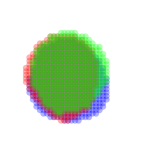

```mathematica
Graphics[{Opacity[0.3],PointSize[0.03],Blue,Point@pts1,Red,Point@pts2,Green,Point@pts3},PlotRange->{{0,280},{0,280}},ImageSize->150]
```

```mathematica
{rotatedm1,rotatedm2,rotatedm3}=ImageRotate[#,Pi/2]&/@{m1,m2,m3};
```

```mathematica
Show[ImageRotate[mask1,Pi/2],Graphics[{XYZColor[0,1,1,0.5],PointSize[0.025],Point@pts1}],ImageSize-> Tiny]
```

-Graphics-

```mathematica
Show[ImageRotate[mask2,Pi/2],Graphics[{Green,Point@pts2}],ImageSize->Tiny]
```

-Graphics-

```mathematica
Show[ImageRotate[mask3,Pi/2],Graphics[{Red,Point@pts3}],ImageSize->Tiny]
```

-Graphics-

```mathematica
(*translate and rotate pts -> this is because of how we created m3 and m2 *)
```

```mathematica
transformPts[image_,pts_,θ_]:=Block[{centim,dxy,ptsR,ptsTR},
centim=ImageMeasurements[image,"IntensityCentroid"];
ptsR= RotationTransform[θ][pts];
dxy=centim-Mean[ptsR];
ptsTR=#+dxy&/@ptsR
];
```

```mathematica
(*translate points from reference image for translation (image padding) *)
```

```mathematica
centrotatedRef=ImageMeasurements[rotatedm1,"IntensityCentroid"];
meanRefPts=N[Mean@pts1];
dxy=centrotatedRef-meanRefPts;
pts1F=transformPts[rotatedm1,pts1,0.];
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[0,1,1,0.75],Point@pts1F}],ImageSize->Small]
```

-Graphics-

```mathematica
(*rotate and translate points to align with reference *)
```

```mathematica
pts3TR=transformPts[rotatedm3,pts3,-π/4.0];
Show[rotatedm3,Graphics[{Blue,Point@pts3TR}],ImageSize->Small]
```

-Graphics-

```mathematica
(*now apply the geometric transform to diffuse flowfield within the reference bounds *)
```

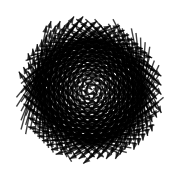

```mathematica
Graphics[{XYZColor[0,0,0,0.75],Arrowheads[Tiny],Arrow/@Thread[{pts3TR,RotationTransform[-π/2.0,Mean@pts3TR]@pts3TR}]},ImageSize->Small]
```

```mathematica
pts3F=(RotationTransform[π/2,Mean@#][#])&@transF2[RotationTransform[-π/2,Mean@pts3TR]@pts3TR];
Show[rotatedm3,Graphics[{Blue,Point@pts3TR,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize-> 200]
```

-Graphics-

```mathematica
(*the pts from the image transform well onto the reference *)
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],Cyan,Point@pts1F,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize->Small]
```

-Graphics-

```mathematica
(*rotate and translate points to align with reference *)
```

```mathematica
pts2TR=transformPts[rotatedm2,pts2,-2.2/5π];
Show[rotatedm2,Graphics[{Blue,Point@pts2TR}],ImageSize->Small]
```

-Graphics-

```mathematica
(*now apply the geometric transform *)
```

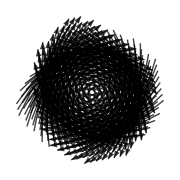

```mathematica
Graphics[{XYZColor[0,0,0,0.75],Arrowheads[Tiny],Arrow/@Thread[{pts2TR,RotationTransform[-π/2.0,Mean@pts2TR]@pts2TR}]},ImageSize->Small]
```

```mathematica
pts2F=(RotationTransform[π/2,Mean@#][#])&@transF1[RotationTransform[-π/2,Mean@pts2TR]@pts2TR];
Show[rotatedm2,Graphics[{Blue,Point@pts2TR,XYZColor[1,0,0,0.75],Point@pts2F}],ImageSize-> 200]
```

-Graphics-

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[1,0,0,0.75],Point@pts2F,Cyan,Point@pts1F}],ImageSize->250]
```

-Graphics-

```mathematica
(*the pts from the image transforms  well onto the reference *)
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[1,0,0,0.75],Point@pts2F,Cyan,Point@pts1F,,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize->250]
```

-Graphics-

### Velocity Profile

```mathematica
flowfieldref=Thread[{pts1F,vec1}];
```

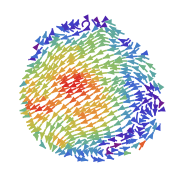

```mathematica
plt1=With[{reg=ConvexHullMesh[flowfieldref[[All,1]]]},
ListStreamPlot[flowfieldref,RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],
StreamPoints->Fine,StreamColorFunction->"Rainbow",StreamStyle->Thickness[0.006],
ImageSize->Small,Frame->False]
]
```

```mathematica
θ1=UnitConvert[Quantity[VectorAngle[Mean@flowfieldref[[All,-1]],Mean@vec2],"Radians"],"Degrees"]
```

83.0575 °

```mathematica
flow2=MapAt[RotationTransform[-θ1],Thread[{pts2F,vec2}],{All,2}];
```

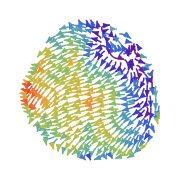

```mathematica
plt2=With[{reg=ConvexHullMesh[flow2[[All,1]]]},
ListStreamPlot[flow2,RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],
StreamPoints->Fine,StreamColorFunction->"Rainbow",StreamStyle->Thickness[0.006],
ImageSize->Small,Frame->False]
]
```

```mathematica
θ2=UnitConvert[Quantity[VectorAngle[Mean@flowfieldref[[All,-1]],Mean@vec3],"Radians"],"Degrees"]
```

59.7681 °

```mathematica
flow3=MapAt[RotationTransform[-θ2],Thread[{pts3F,vec3}],{All,2}];
```

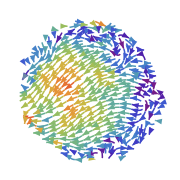

```mathematica
plt3=With[{reg=ConvexHullMesh[flow3[[All,1]]]},
ListStreamPlot[flow3,RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],
StreamPoints->Fine,StreamColorFunction->"Rainbow",StreamStyle->Thickness[0.006],
ImageSize->Small,Frame->False]
]
```

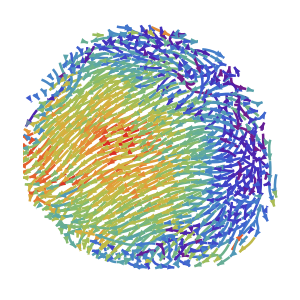

```mathematica
Show[plt1,plt2,plt3,ImageSize->300]
```

```mathematica
totalflow=flowfieldref~Join~flow2~Join~flow3;
meanflow=Normal@GroupBy[totalflow,First-> Last,Mean]/. Rule -> List;
meanflowF=Thread[{(x↦x-dxy)/@#[[1]],#[[2]] }]&@Transpose[meanflow];
```

```mathematica
midimage=Ceiling[1/2Length[images]];
With[{reg=ConvexHullMesh@meanflowF[[All,1]]},
Image[ImageRotate[
Rasterize[Show[
ImageRotate[SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[masks1[[5]],10],"Real"],.5]],Pi/2],
ListStreamPlot[meanflowF,RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],
StreamPoints->Fine,StreamColorFunction->"Rainbow",StreamStyle->Thickness[0.006]],
ImageSize->Large],"Image",ImageResolution->500],
-Pi/2],ImageSize->Medium]
]
```

-Graphics-

```mathematica
(*DumpSave["C:\\Users\\aliha\\Desktop\\optic flow\\meanflow.mx",meanflowF]*)
```

### 2D Interpolation of velocity field & velocity along polarization vector

```mathematica
flowfF=Normal@GroupBy[MapAt[N[#,1]&,meanflowF,{All,1}],First-> Last,Mean]/.Rule-> List;
meanflowfU=Normal@GroupBy[Thread[{N@Round[flowfF[[All,1]]],flowfF[[All,2,1]]}],First-> Last,Mean]/.Rule-> List;
meanflowfV=Normal@GroupBy[Thread[{N@Round[flowfF[[All,1]]],flowfF[[All,2,2]]}],First-> Last,Mean]/.Rule-> List;
```

```mathematica
interpU =Interpolation[meanflowfU,InterpolationOrder->1]
interpV =Interpolation[meanflowfV,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

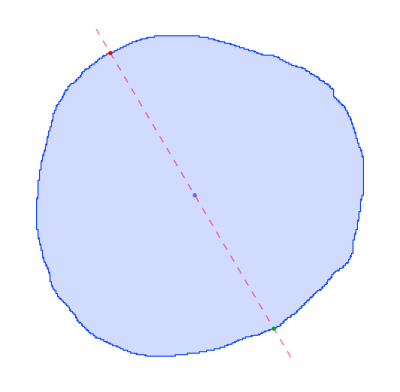
{-Graphics-,{124.966,120.063},{68.4717,215.472},{178.,30.4987},{28.,62.646},{225.442,179.558}}

```mathematica
{graphics,c,c1,c2,c3,c4}=bisectMask[mask1,True]
```

```mathematica
polLine=bresenhamLine[Round@c4,Round@c3];
Show[ImageRotate[mask1,Pi/2],Graphics[{PointSize[0.035],Orange,Point@Round[c3],Darker@Green,Point@Round[c4],Thick,
Red,Thickness[0.012],Arrowheads[Large],Arrow@First@TakeDrop[polLine,{28,-30}],
PointSize[0.015],XYZColor[0,0,1,0.5],Point@flowfF[[All,1]]}]]
```

-Graphics-

```mathematica
polLine=First@TakeDrop[polLine,{28,-30}];
upol=Quiet[interpU@@#&/@polLine];
vpol=Quiet[interpV@@#&/@polLine];
v=Thread[{upol,vpol}];
truncateFlow=(Norm/@v);
```

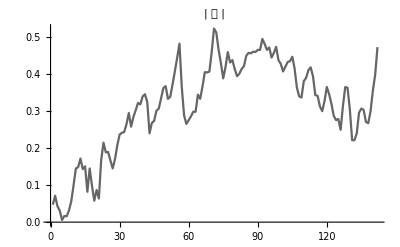

```mathematica
ListLinePlot[truncateFlow,PlotStyle-> XYZColor[0,0,0,0.6],PlotRange->Full,
PlotLabel->Style["| 𝒱 |",Bold,Blue,16]]
```

```mathematica
Clear[fit,model];
Off[NonlinearModelFit::sszero];
model=a/(1+Exp[((d-p)-x)/b]);
fit=NonlinearModelFit[truncateFlow,model,{a,{p,20},b,{d,100}},x]
On[NonlinearModelFit::sszero];
```

FittedModel[0.382816/(1+ⅇ^(0.0936707 (26.0432-x)))]

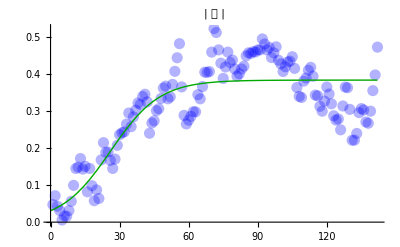

```mathematica
Show[
ListPlot[truncateFlow,PlotStyle-> {Opacity[0.3],Blue,PointSize[0.02]},PlotRange->Full,
PlotLabel->Style["| 𝒱 |",Bold,Blue,16]],Plot[fit[x],{x,0,Length@truncateFlow},
PlotStyle->{Darker@Green,Thick}]
]
```

```mathematica
𝒬=With[{ρ=Quantity[1000, ("Kilograms")/(("Meters")^3 "Seconds")],binningratio=2,resolution=Quantity[0.633, "Micrometers"],L=Quantity[50, "Micrometers"],time=6 60},
ρ*(binningratio*resolution)*(1/L)*(fit[Length@truncateFlow]/time)
]
```

0.0269242 kg/(m^3 s)

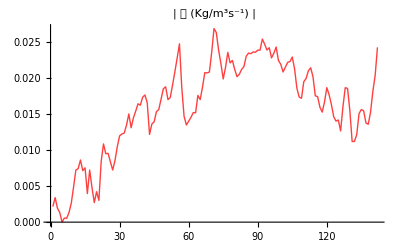

```mathematica
ListLinePlot[𝒬 Rescale@truncateFlow,PlotStyle-> {Opacity[0.75],Red,Thick},PlotRange->Full,
PlotLabel->Style["| 𝒬 (Kg/m^3s^-1) |",Italic,Blue,16]]
```

## Velocity Gradient ∇ | Strain Rate

```mathematica
SetAttributes[makeVecs,HoldAll];
makeVecs[vals_,vecs_,s_,rQ_]:=With[{n=Length[vals]},If[TrueQ[rQ],Do[Switch[Sign[Im[vals[[k]]]],0,Null,1,vecs[[k]]+=s I vecs[[k+1]],-1,vecs[[k]]=Conjugate[vecs[[k-1]]]],{k,n}]]]

Options[getEigensystem]={Mode->Automatic};

getEigensystem[mat_?SquareMatrixQ,opts:OptionsPattern[]]:=Module[{m=mat,chk,ei,ev,lm,lv,n,rm,rQ,rv},

n=Length[mat];
Switch[OptionValue[Mode],
Right|Automatic,
{lm,rm}={"N","V"},
Left,{lm,rm}={"V","N"},
All,{lm,rm}={"V","V"},
_,{lm,rm}={"N","V"}];
LinearAlgebra`LAPACK`GEEV[lm,rm,m,ev,ei,lv,rv,chk,rQ];
If[!TrueQ[chk],
Message[getEigensystem::eivec0];
Return[$Failed,Module]
];
If[rQ,ev+=I ei];
Switch[OptionValue[Mode],Right|Automatic,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv},Left,lv=ConjugateTranspose[lv];
makeVecs[ev,lv,-1,rQ];{ev,lv},All,{lv,rv}=ConjugateTranspose/@{lv,rv};
makeVecs[ev,rv,1,rQ];makeVecs[ev,lv,-1,rQ];
{ev,rv,lv},_,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv}]
];
```

```mathematica
Clear@meshgrid;
meshgrid[int1_Integer,int2_Integer]:=Transpose[
{ConstantArray[Range[int1],int2],Transpose@ConstantArray[Range[int2],int1]},
{3,2,1}];
meshgrid[list1_List,list2_List]:=Transpose[
{ConstantArray[list1,Length@list2], Transpose@ConstantArray[list2,Length@list1]},
{3,2,1}];
```

```mathematica
Unprotect[None,Power];
None/:Subtract[None,None]:=None;
None/:Subtract[None,_Real|_Integer]:=None;
None/:Subtract[_Real|_Integer,None]:=None;
None/:Plus[None,-None]:=None;
None/:Plus[None,_Real|_Integer]:=None;
None/:Times[Rational[_,_],None]:=None;
None/:Times[_Integer|_Real,None]:=None;
None/:Times[None,None]:=None;
Power/:Times[_,Power[None,_]]:=None;
Protect[None,Power];
```

```mathematica
Unevaluated[x]/:grad[Unevaluated[x],array_,div_]:=Block[{arr,nx,ny,diffL,diffR,diff},
{nx,ny}={#[[1]],#[[2]]}&[Dimensions[array]];
arr=PadLeft[PadRight[array,{nx,ny+1},None],{nx,ny+2},None];
diffL=arr[[All,2;;ny+1]]-arr[[All,1;;ny]];
diffR=arr[[All,3;;ny+2]]-arr[[All,2;;ny+1]];
diff=(diffL+diffR)/2;
diff/div
];
Unevaluated[y]/:grad[Unevaluated[y],array_,div_]:=Block[{arr,nx,ny,diffL,diffR,diff},
{nx,ny}={#[[1]],#[[2]]}&[Dimensions[array]];
arr=PadLeft[PadRight[array,{nx+1,ny},None],{nx+2,ny},None];
diffL=arr[[2;;nx+1,All]]-arr[[1;;nx,All]];
diffR=arr[[3;;nx+2,All]]-arr[[2;;nx+1,All]];
diff=(diffL+diffR)/2;
diff/div
];
```

```mathematica
pts=Round@flowfF[[All,1]];
{ymin,ymax}=MinMax@pts[[All,1]];
{xmin,xmax}=MinMax@pts[[All,2]];
array=meshgrid[Range[ymin,ymax],Range[xmin,xmax]];
```

```mathematica
allpts=Flatten[array,1];
ptsinDomain=Pick[allpts,RegionMember[ConvexHullMesh@pts][allpts],True];
flowinDomain=Thread[{ptsinDomain,Transpose[Apply[#,ptsinDomain,{1}]&/@{interpU,interpV}]}];
```

```mathematica
dgrad=dgrid=8;
{pts,vel}=flowinDomainᵀ;
{ymin,ymax}=MinMax@pts[[All,1]];
{xmin,xmax}=MinMax@pts[[All,2]];
array=meshgrid[Range[ymin,ymax,dgrid],Range[xmin,xmax,dgrid]];
gridpts=Flatten[array,1]∩flowinDomain[[All,1]];
{ny,nx}={#[[1]],#[[2]]}&[Dimensions[array]];
```

```mathematica
grid=Replace[Replace[array,Dispatch[Thread[pts->vel]],{2}],{__Integer} -> {None,None},{2}];
```

```mathematica
(*ux,vx,uy,vy*)
ux=grad[Unevaluated[x],grid[[All,All,2]],dgrad];
vx=grad[Unevaluated[x],grid[[All,All,1]],dgrad];
uy=grad[Unevaluated[y],grid[[All,All,2]],dgrad];
vy=grad[Unevaluated[y],grid[[All,All,1]],dgrad];
```

```mathematica
DVxx = (ux);
DVyx=DVxy =(uy+vx)/2;
DVyy=(vy);
DVww=(-uy+vx); (*rotation*)
trace=(DVxx+DVyy)/2;
```

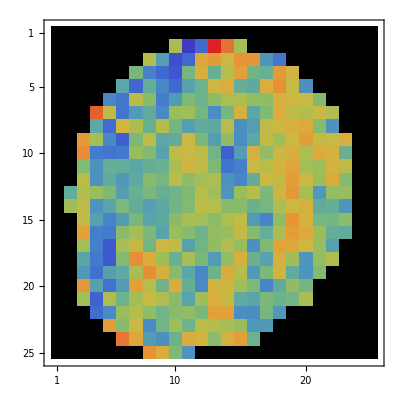
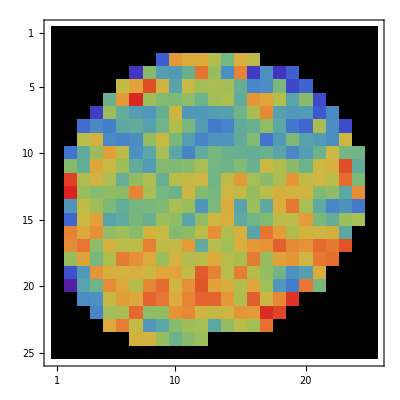
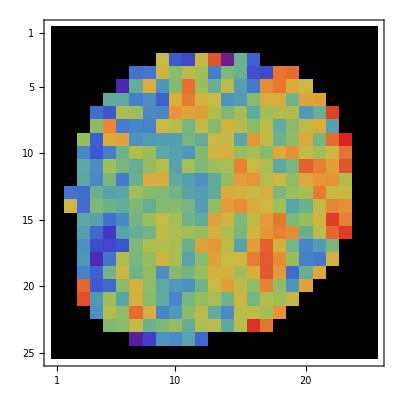
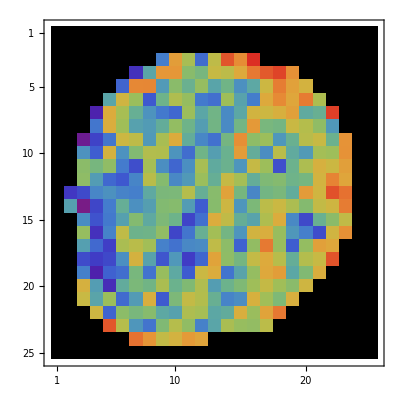
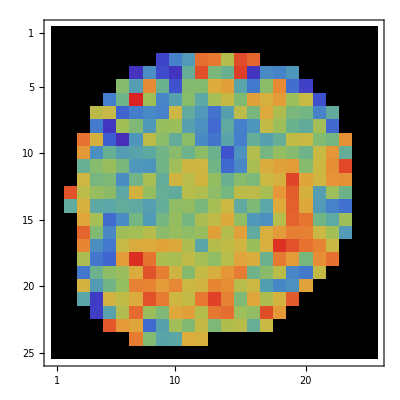
{xx→-Graphics-,yy→-Graphics-,yx→-Graphics-,xy→-Graphics-,ww→-Graphics-,trace→-Graphics-}

```mathematica
Thread[{"xx","yy","yx","xy","ww","trace"}->(MatrixPlot[#,ColorFunction->"Rainbow",ColorRules->{0->Black}]&/@({DVxx,DVyy,DVyx,DVxy,DVww,trace}/.None-> 0))]
```

```mathematica
ColorData["CandyColors"]
```

ColorDataFunction[…]

```mathematica
pos=SparseArray[(DVxx*DVyy*DVxy)/.None->0]["NonzeroPositions"];
```

```mathematica
Clear@plotbars;
With[{imgdim2=Last@ImageDimensions[images[[1]]]},
plotbars[ϕ_,eigval_,scale_,inds_]:=Module[{Amp,x0,y0,xmaj,ymaj},
Amp=scale Abs[eigval];
{y0,x0}=array[[Sequence@@inds]];
{xmaj,ymaj}=Amp Through[{Cos,Sin}[ϕ]];
Line[Abs[{0,imgdim2}-{##}]&@@@Thread[{xmaj {-1,1}+x0,ymaj {-1,1}+y0}]]
]
];
```

```mathematica
midimage=Ceiling[3/4 Length[images]];
ptsTransfer=With[{imgdim=Last@ImageDimensions[images[[midimage]]]},
{#[[2]],imgdim-#[[1]]}&/@gridpts
];
```

```mathematica
HighlightImage[images[[midimage]],{Opacity[0.5],gridpts,Blue,ptsTransfer}]
```

-Graphics-

```mathematica
{err,transFnPts}=FindGeometricTransform[ptsTransfer,gridpts]
```

{3.53472×10^-14,TransformationFunction[(-2.77556×10^-16 | 1. | 8.52651×10^-14
-1. | -3.33067×10^-16 | 244.
0. | 0. | 1.)]}

```mathematica
{pt,dir}=Mean/@{N@meanflow[[All,1]],meanflow[[All,2]]};
θ=(ArcTan[#[[2]]/#[[1]]]&[dir]);
graphicsPrimitive={};
Do[
DV={{(DVxx[[Sequence@@i]]-DVyy[[Sequence@@i]])/2,DVxy[[Sequence@@i]]},
{DVxy[[Sequence@@i]],-(DVxx[[Sequence@@i]]-DVyy[[Sequence@@i]])/2 }}; 

If[FreeQ[DV,None],
(*{eVa,eVe}={DiagonalMatrix[#[[1]]],#[[2]]}&@Eigensystem[DV];*)
{eVa,eVe}={DiagonalMatrix[Reverse@#[[1]]],Reverse[-#[[2]]]}&[Re@getEigensystem[DV]];
vp1=Diagonal[eVa];
{val1,ind1}={Sort@vp1,Ordering@vp1};
ϕ= ArcTan[eVe[[2,ind1[[2]] ]]/eVe[[1,ind1[[2]] ]] ];
rvect={eVe[[1,ind1[[2]] ]],eVe[[2,ind1[[2]] ]]};

rotationTrans=RotationTransform[θ];
rvectTurned=rotationTrans[rvect];
scalar=Abs[First@rvectTurned];

{minDv,maxDv} = MinMax[eVa];
Tracee = (DVxx[[Sequence@@i]]+DVyy[[Sequence@@i]])/2;

Block[{prim},
If[Abs[minDv]*Abs[maxDv]>0,
prim=GeometricTransformation[
Circle[transFnPts@array[[Sequence@@i]],{Round[500Abs[Tracee]],Round[Abs[500 Tracee]]}],
RotationTransform[ϕ,transFnPts@array[[Sequence@@i]]]
];
If[Tracee>0,
(*isotropic strain-rate*)
AppendTo[graphicsPrimitive,{prim}~Prepend~XYZColor[1,0,0,0.5]],
AppendTo[graphicsPrimitive,{prim}~Prepend~XYZColor[0,0,1,0.5]]
];
(*anisotropic strain-rate*)
AppendTo[graphicsPrimitive,
{ColorData["CandyColors"][scalar],Thickness[0.005],plotbars[ϕ,maxDv,500,i]}]
]
]
],{i,pos}]
```

```mathematica
ptsVelAssoc=AssociationThread[flowinDomain[[All,1]],flowinDomain[[All,-1]]];
transVec=TransformationFunction[ReplacePart[Chop@transFnPts[[1]],{2,3}->0]];
meanflowRot=Thread[{ptsTransfer,transVec[#]&/@Lookup[ptsVelAssoc,gridpts]}];
{pt,dir}=Mean/@{N@meanflowRot[[All,1]],meanflowRot[[All,2]]};
```

```mathematica
midimage=Ceiling[1/2 Length[images]];
Image[
Rasterize[Show[
SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[masks1[[5]],10],"Real"],.5]],
Graphics[If[!FreeQ[#,0,Infinity],{Thick,#},{Thin,#}]&/@graphicsPrimitive],
Graphics[{GrayLevel[0],Thick,Arrowheads[{{.035,1,{-Graphics-,1}}}],Arrow[{pt,(pt+200dir)}]}],
ImageSize->Large],"Image",ImageResolution->500],
ImageSize->500]
```

-Graphics-